## Calculations

```mathematica
(*θ=30°;*)
(*θ=40°;*)
(*cardSizeXY={29.60,38.55};*)
cardSizeXY={cardSizeX,cardSizeY};
(*ejectorAxleRadius=2;*)
ejectorAxleCenter=cardSizeXY*{9/20,1}+{0,ejectorAxleRadius};
```

```mathematica
leverBottom=TranslationTransform[ejectorAxleCenter]@RotationTransform[θ]@InfiniteLine[{0,-ejectorAxleRadius},{1,0}]
```

InfiniteLine[{(9 cardSizeX)/20+ejectorAxleRadius Sin[θ],cardSizeY+ejectorAxleRadius-ejectorAxleRadius Cos[θ]},{Cos[θ],Sin[θ]}]

```mathematica
(*springWidth=2;
wallWidthForEjectorChute=3;
ejectorChuteWidthX=4;*)
```

```mathematica
plungerAnchor=cardSizeXY*{1/2,1}+{springWidth+wallWidthForEjectorChute+ejectorChuteWidthX/2,0}
```

{cardSizeX/2+ejectorChuteWidthX/2+springWidth+wallWidthForEjectorChute,cardSizeY}

```mathematica
plungerEndRadius=ejectorChuteWidthX/2;
```

```mathematica
leverCircleCenterGuide=TranslationTransform[ejectorAxleCenter]@RotationTransform[θ]@TranslationTransform[{0,-ejectorAxleRadius-plungerEndRadius}]@InfiniteLine[{1,0}]
```

InfiniteLine[{(9 cardSizeX)/20-1/2 (-2 ejectorAxleRadius-ejectorChuteWidthX) Sin[θ],cardSizeY+ejectorAxleRadius+1/2 (-2 ejectorAxleRadius-ejectorChuteWidthX) Cos[θ]},{Cos[θ],Sin[θ]}]

```mathematica
plungerCircleCenterGuide=InfiniteLine[plungerAnchor,{0,1}]
```

InfiniteLine[{cardSizeX/2+ejectorChuteWidthX/2+springWidth+wallWidthForEjectorChute,cardSizeY},{0,1}]

```mathematica
extraInternalDepthForEjector=7.3;
```

```mathematica
Param[a_,InfiniteLine[{pX_,pY_},{dX_,dY_}]]:={pX+a*dX,pY+a*dY}
```

```mathematica
Param[a,leverCircleCenterGuide]
```

{(9 cardSizeX)/20+a Cos[θ]-1/2 (-2 ejectorAxleRadius-ejectorChuteWidthX) Sin[θ],cardSizeY+ejectorAxleRadius+1/2 (-2 ejectorAxleRadius-ejectorChuteWidthX) Cos[θ]+a Sin[θ]}

```mathematica
Param[b,plungerCircleCenterGuide]
```

{cardSizeX/2+ejectorChuteWidthX/2+springWidth+wallWidthForEjectorChute,b+cardSizeY}

```mathematica
plungerEndRadiusCenterAB=Solve[Param[a,leverCircleCenterGuide]==Param[b,plungerCircleCenterGuide],{a,b}][[1]]
```

{a→1/20 (cardSizeX Sec[θ]+10 ejectorChuteWidthX Sec[θ]+20 springWidth Sec[θ]+20 wallWidthForEjectorChute Sec[θ]-20 ejectorAxleRadius Tan[θ]-10 ejectorChuteWidthX Tan[θ]),b→1/20 (20 ejectorAxleRadius-20 ejectorAxleRadius Cos[θ]-10 ejectorChuteWidthX Cos[θ]+cardSizeX Tan[θ]+10 ejectorChuteWidthX Tan[θ]+20 springWidth Tan[θ]+20 wallWidthForEjectorChute Tan[θ]-20 ejectorAxleRadius Sin[θ] Tan[θ]-10 ejectorChuteWidthX Sin[θ] Tan[θ])}

```mathematica
plungerEndRadiusCenter=(Param[a,leverCircleCenterGuide]/.plungerEndRadiusCenterAB)//Simplify
```

{1/2 (cardSizeX+ejectorChuteWidthX+2 (springWidth+wallWidthForEjectorChute)),cardSizeY+ejectorAxleRadius-1/2 (2 ejectorAxleRadius+ejectorChuteWidthX) Sec[θ]+(cardSizeX/20+ejectorChuteWidthX/2+springWidth+wallWidthForEjectorChute) Tan[θ]}

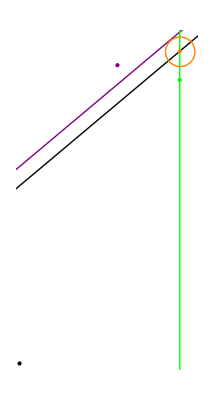

```mathematica
Graphics[{
Point[{0,0}],
{Purple,leverBottom},
leverCircleCenterGuide,
{Purple,Point@ejectorAxleCenter},
TranslationTransform[plungerAnchor+{0,extraInternalDepthForEjector}][InfiniteLine[{1,0}]],
{Green,Point@plungerAnchor},
{Green,plungerCircleCenterGuide},
{Orange,Point@plungerEndRadiusCenter},
{Orange,Circle[plungerEndRadiusCenter,plungerEndRadius]}
}/.{θ->40°,cardSizeX->29.60,cardSizeY->38.55,springWidth->2,wallWidthForEjectorChute->3,ejectorChuteWidthX->4,ejectorAxleRadius->2}]
```